```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

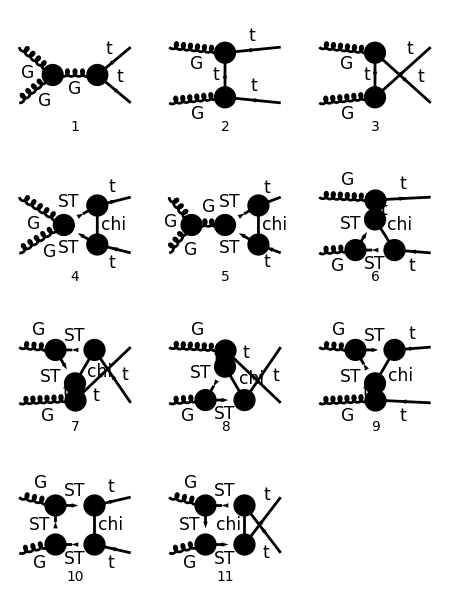

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
(* goodDiags=DiagramExtract[goodDiags,{1,5}]; *)
(* goodDiags=DiagramExtract[goodDiags,{10,11}]; *) 
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 450,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True, SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},TransversePolarizationVectors->{k1,k2}, LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames->{μ,ν}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]];
(* Remove terms of higher order *)
ampB = Normal[Series[ampB,{yDM,0,2},{gs,0,2}]];
```

in total: 11 Particles amplitudes

```mathematica
ampC =Simplify[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])];
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampD=Simplify[ampC-ampSM];
(* ampD=ampD/.{PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C00,PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C11,PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C12,PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C1}; *)
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DiracSimplify[ampD]/.{s+t+u-> 2 MT^2}];
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp,PaVe]]}];
```

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp,deltaCTR]] (-1/(4 EpsilonUV));
FullSimplify[loopUV+ctUV]
```

0

## Tensor Structure

```mathematica
PVsubs =Flatten[Table[PaVe[a,{0,b,MT^2,s,MT^2,0},c__]->ToExpression[StringJoin[ "D",ToString[a],ToString[b]]],{a,0,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{0,b,MT^2,s,MT^2,0},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[b]]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{0,b,MT^2,s,MT^2,0},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],ToString[b]]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
```

```mathematica
ampEsimp2=DiracSimplify[ampEsimp/.PVsubs/.{DiracGamma[7]->1-DiracGamma[6]}];
```

```mathematica
pairs=Cases2[ampEsimp2,Pair]
sps=Cases2[ampEsimp2,Spinor]
gams=Cases2[ampEsimp2,DiracGamma]
allTerms=Join[Table[sps[[1]].gams[[i]].sps[[2]],{i,Length[gams]}],Flatten[Table[sps[[1]].gams[[i]].gams[[j]].sps[[2]],{i,Length[gams]},{j,Length[gams]}]]];
```

{k1·ε(k2),k2·ε(k1),p1·ε(k1),p1·ε(k2),p2·ε(k1),p2·ε(k2),ε(k1)·ε(k2)}

{φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,γ·k1,γ·k2,γ·ε(k1),γ·ε(k2)}

```mathematica
ampEsimp3=Collect[ampEsimp2,allTerms,FullSimplify];
```

## EFT Limit

```mathematica
loopInts =Cases2[ampEsimp,PaVe];
loopIntsEFT=Table[{loopInts[[i]],Collect[PaXEvaluate[loopInts[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0},{t,0,0},{u,0,0}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},{Epsilon},FullSimplify]},{i,1,Length[loopInts]}];
```

```mathematica
deltaCTLeft=FullSimplify[Normal[Series[((1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])))//.{xT-> MT^2/mST^2,xC->mChi^2/mST^2,lA-> 1+xC^2+xT^2-2*xC-2*xT-2*xT*xC},{MT,0,0}]],Assumptions->{mChi>0,mST>0,mST>mChi}]
deltaCTReft=FullSimplify[Normal[Series[((1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])))//.{xT-> MT^2/mST^2,xC->mChi^2/mST^2,lA-> 1+xC^2+xT^2-2*xC-2*xT-2*xT*xC},{MT,0,0}]],Assumptions->{mChi>0,mST>0,mST>mChi}]
```

0

-(-4 mChi^2 mST^2-4 mChi^4 log(mChi/mST)+3 mChi^4+mST^4)/(128 π^4 (mChi^2-mST^2)^2)

```mathematica
ampEFT =Simplify[ampEsimp/.Table[loopIntsEFT[[i,1]]-> loopIntsEFT[[i,2]],{i,1,Length[loopIntsEFT]}]/.{deltaCTL->deltaCTLeft,deltaCTR->deltaCTReft}];
```

```mathematica
ampEFT
```

(gs^2 π^2 1 (20 1 (-1/(ε 2 1^2)-1+ⅈ t (1+1))+1))/(5760 t u)
 |  |  |  |

```mathematica
ampEFT2=FullSimplify[Normal[Series[ampEFT,{s,0,0},{t,0,0},{u,0,0}]],Assumptions->{mChi>0,mST>0,mST>mChi}]
```

-(ⅈ gs^2 π^2 yDM^2 (-B_0(0,mChi^2,mST^2) mChi^2+A_0(mChi^2)-A_0(mST^2)+mST^2 B_0(0,mChi^2,mST^2)) (φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/(t ((k2-p2)^2-MT^2))+(ⅈ gs^2 π^2 3 (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/(u ((k2-p1)^2-MT^2))+(gs^2 π^2 (436+20 1 (1)) yDM^2)/5760
 |  |  |  |